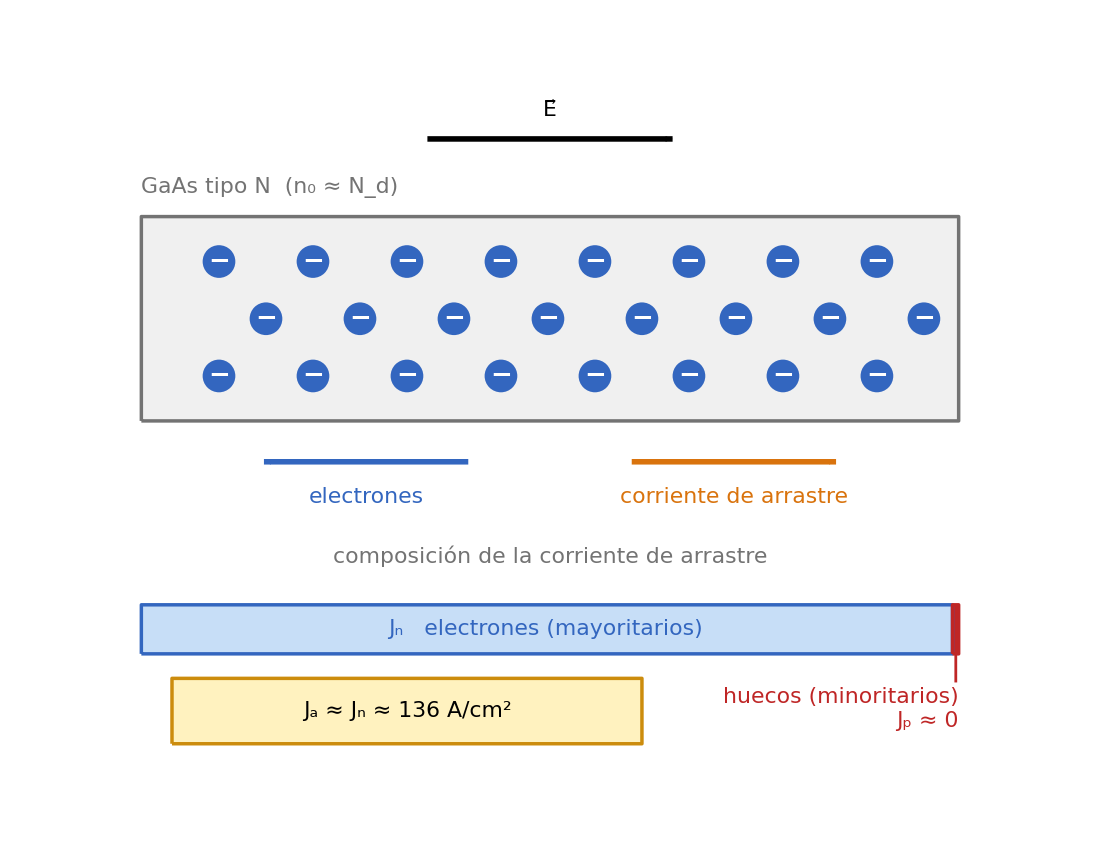

```mathematica
diagramaArrastreGaAs = Module[
  {fs, mostrarValor, cAzulB, cClaro, cRojo, cNar, cGris, cOro, cOroB,
   e, muN, Nd, Eapl, ja, res, ins, insI, insD, flecha, caja, electron},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValor = True;     (* False oculta el valor numérico de J_a *)
  cAzulB = RGBColor[0.20, 0.40, 0.75];  cClaro = RGBColor[0.78, 0.87, 0.97];
  cRojo  = RGBColor[0.75, 0.15, 0.15];  cNar   = RGBColor[0.85, 0.45, 0.05];
  cGris  = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del ejemplo (SI en cm, V, s) ---------- *)
  e = 1.6*10^-19;  muN = 8500;  Nd = 10^16;  Eapl = 10;
  ja = Round[e muN Nd Eapl];     (* J_a ≈ e μn Nd E, en A/cm^2 *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.025], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  electron[pos_] :=
    {cAzulB, Disk[pos, 0.4],
     Text[Style["−", Round[1.2 fs], Bold, White], pos]};

  res = If[mostrarValor,
    Row[{Subscript["J", "a"], " ≈ ", Subscript["J", "n"],
      " ≈ ", ja, " A/", Superscript["cm", 2]}],
    Row[{Subscript["J", "a"], " ≈ ", Subscript["J", "n"]}]];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* semiconductor tipo N *)
    {GrayLevel[0.94], EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{1, 8}, {21, 13}]},
    insI[Row[{"GaAs tipo N  (", Subscript["n", 0], " ≈ ",
       Subscript["N", "d"], ")"}], {1, 13.7}, cGris],

    (* electrones mayoritarios *)
    Table[electron[{2.9 + 2.3 i + 1.15 Mod[k, 2], 9.1 + 1.4 k}],
     {k, 0, 2}, {i, 0, 7}],

    (* campo eléctrico aplicado *)
    flecha[{8, 14.9}, {14, 14.9}, Black],
    ins[Row[{OverVector["E"]}], {11, 15.6}],

    (* sentido de los electrones y de la corriente *)
    flecha[{9, 7}, {4, 7}, cAzulB],
    ins["electrones", {6.5, 6.15}, cAzulB],
    flecha[{13, 7}, {18, 7}, cNar],
    ins["corriente de arrastre", {15.5, 6.15}, cNar],

    (* composición de la corriente de arrastre *)
    ins["composición de la corriente de arrastre", {11, 4.7}, cGris],
    {EdgeForm[{AbsoluteThickness[2.5], cAzulB}], cClaro,
     Rectangle[{1, 2.3}, {20.85, 3.5}]},
    {EdgeForm[{AbsoluteThickness[2.5], cRojo}], cRojo,
     Rectangle[{20.85, 2.3}, {21, 3.5}]},
    ins[Row[{Subscript["J", "n"], "   electrones (mayoritarios)"}], {10.9, 2.9}, cAzulB],
    {cRojo, AbsoluteThickness[2], Line[{{20.93, 2.3}, {20.93, 1.6}}]},
    insD[Column[{"huecos (minoritarios)",
       Row[{Subscript["J", "p"], " ≈ 0"}]}, Right], {21, 0.95}, cRojo],

    (* resultado *)
    caja[{7.5, 0.9}, {11.5, 1.6}, cOro, cOroB],
    ins[res, {7.5, 0.9}]
   },
   ImageSize -> 1100,
   PlotRange -> {{0, 22}, {-0.6, 16.4}},
   PlotRangePadding -> None,
   AspectRatio -> 17/22,
   Background -> White]
];
diagramaArrastreGaAs
```